# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order3_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles[[1]]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse2\1) Fitting Scale\Export

# Parametrization of the Lobe’s Flattening Factor σ_n

```mathematica
paramsFlat = Table[Table[rawFiles[[albedo]][[j]][[i]][[4]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsFlat[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsFlat[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsFlat[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Green],
ListPlot3D[paramsFlat[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Yellow]
 ]
```

-Graphics3D-

We see that for most albedo values, the shape is very similar and there is no dependency on the albedo at all, which is good (only the global scale factor σ should be dependent on albed).
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in α is from index 1 to about 8.
There is also a slight inflection of the curve for grazing angles indicating a slight dependency on θ.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

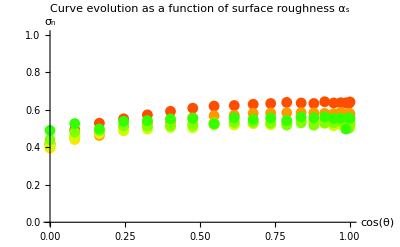

```mathematica
paramsFlat0=paramsFlat[[1]]; (* We only work on albedo = 1 *)
parmsFlatCurves= Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,6}];
Show[Table[ListPlot[parmsFlatCurves[[j]],PlotRange->{0,1},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ_n"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,6}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,6}];
MatrixForm[fittingCurvatures]
```

(a→0.428994 | b→0.669972 | c→-0.750619 | d→0.290283
a→0.410778 | b→0.455233 | c→-0.345833 | d→0.0579558
a→0.400446 | b→0.48894 | c→-0.5783 | d→0.226146
a→0.422988 | b→0.329528 | c→-0.329534 | d→0.0962966
a→0.447593 | b→0.32493 | c→-0.432052 | d→0.184174
a→0.4951 | b→0.168129 | c→-0.12984 | d→0.0105209)

Now let’s try and fit the individual parameters using another fitting for each one:

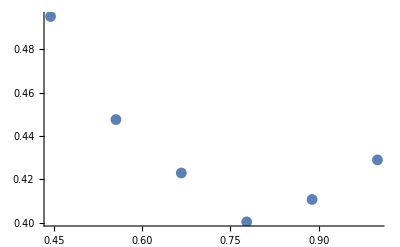

```mathematica
paramsFlatA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,6}];
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,6}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,6}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,6}];
ListPlot[paramsFlatA]
ListPlot[paramsFlatB];
ListPlot[paramsFlatC];
ListPlot[paramsFlatD];
```

Parameter A is the most stable so let’s start with that one...

0.810535-0.92183 α+0.423786 α^2+0.117078 α^3

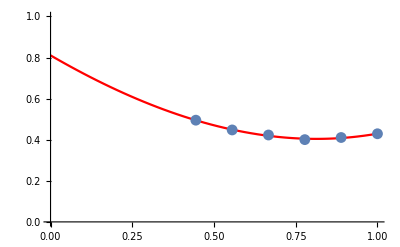

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsFlatA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1}],
ListPlot[paramsFlatA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,6}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0.666077 | c→-0.743456 | d→0.286399
a→0. | b→0.472702 | c→-0.377952 | d→0.075374
a→0. | b→0.458023 | c→-0.521454 | d→0.195318
a→0. | b→0.356425 | c→-0.378988 | d→0.123116
a→0. | b→0.313492 | c→-0.411021 | d→0.172769
a→0. | b→0.170014 | c→-0.133306 | d→0.012401)

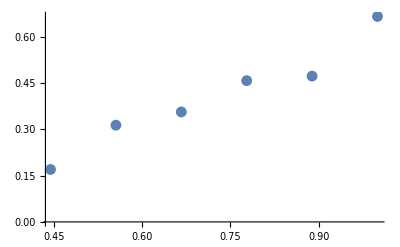

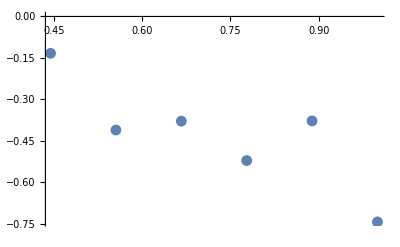

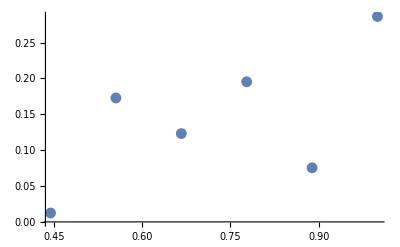

```mathematica
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,6}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,6}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,6}];
ListPlot[paramsFlatB->{0,1}]
ListPlot[paramsFlatC->{-1,0}]
ListPlot[paramsFlatD->{0,1}]
```

We see the model is behaving a little bit better now so we can proceed and fit the next coefficients:

0.311145 α+0.325775 α^2

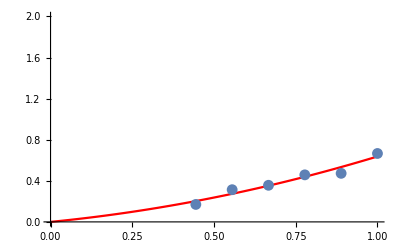

```mathematica
Clear[a,b,c,d]
modelB=0*a+b*u+c*u^2+0*d*u^3;
fittingB = FindFit[ paramsFlatB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{0,2}],
ListPlot[paramsFlatB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,6}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→3.33067×10^-16 | c→-0.662721 | d→0.233757
a→0. | b→2.22045×10^-16 | c→-0.547627 | d→0.186008
a→0. | b→3.33067×10^-16 | c→-0.468988 | d→0.161109
a→0. | b→2.77556×10^-16 | c→-0.367343 | d→0.115523
a→0. | b→1.11022×10^-16 | c→-0.300021 | d→0.100392
a→0. | b→5.55112×10^-17 | c→-0.223644 | d→0.0713041)

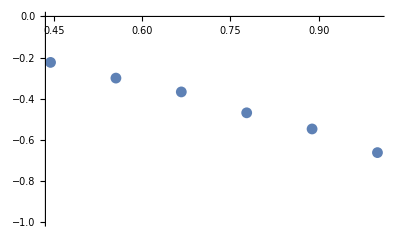

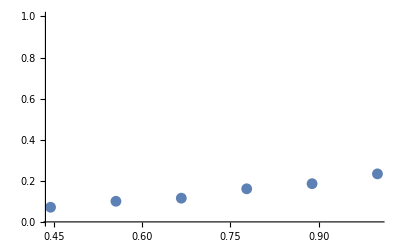

```mathematica
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,6}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,6}];
ListPlot[paramsFlatC,PlotRange->{-1,0}]
ListPlot[paramsFlatD,PlotRange->{0,1}]
```

The model is continuing to improve in stability, let’s keep on replacing...

0.136153-0.781676 α

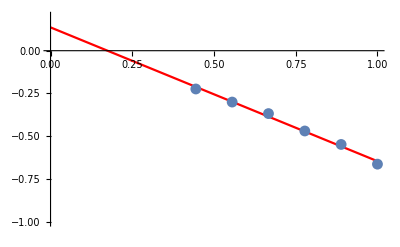

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+0*c*u^2+0*d*u^3;
fittingC = FindFit[ paramsFlatC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-1,0.2}],
ListPlot[paramsFlatC]
]
```

#### Replacing C and Fitting D

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,6}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→0.215186
a→0. | b→0. | c→0. | d→0.197932
a→0. | b→0. | c→0. | d→0.164163
a→0. | b→0. | c→0. | d→0.13455
a→0. | b→0. | c→0. | d→0.0983304
a→0. | b→0. | c→0. | d→0.0579305)

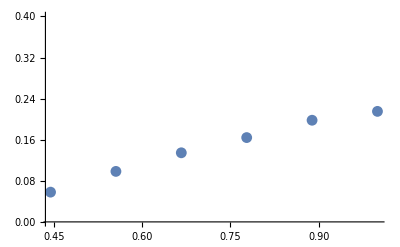

```mathematica
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,6}];
ListPlot[paramsFlatD,PlotRange->{0,0.4}]
```

-0.0623331+0.286636 α

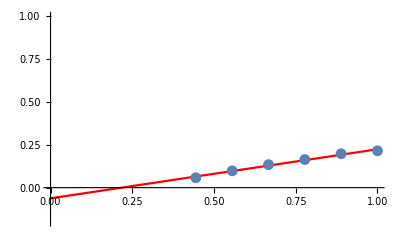

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+0*c*u^2+0*d*u^3;
fittingD = FindFit[ paramsFlatD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{-0.2,1}],
ListPlot[paramsFlatD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)=0.810535-0.92183 α+0.423786 α^2+0.117078 α^3 
	b(α_s)=0.311145 α+0.325775 α^2 
	c(α_s)= 0.136153-0.781676 α
	d(α_s)=-0.0623331+0.286636 α
	
	σ_n(μ,α_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ]
fA[α_]= 0.8105350357857184-0.9218299991502038 α+0.4237861886920572 α^2+0.1170778529748108 α^3;
fB[α_]= 0.31114547597877934 α+0.32577529154291324 α^2;
fC[α_]= 0.1361534489871508-0.7816763659800733 α;
fD[α_]=-0.06233306857442866+0.286636418782464 α;
fFlat[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;

(* Order 2 *)
fA[α_]= 0.9136434030473861-1.6554846256054254 α+1.396170391613371 α^2-0.3203305249468263 α^3;
fB[α_]= 0.044723925680673265+0.6247396225423497 α;
fC[α_]= -0.11884367470512597-0.973212684779483 α+0.36902017638601514 α^2;
fD[α_]=0.13257717032932556+0.1697498085943817 α;
fFlat2[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;

Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];
Show[
Plot3D[fFlat[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ_n"},PlotLabel->"Lobe flattening factor",PlotRange->{0,1}],
Plot3D[fFlat2[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ_n"},PlotLabel->"Lobe flattening factor",PlotRange->{0,1},PlotStyle->Red]
]
```

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fFlat[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

# Parametrization of the lobe’s Scale factor σ

```mathematica
paramsScale = Table[Table[rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScale[[albedo]],{ PlotRange->{0,0.4},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,resZ}]
]
```

-Graphics3D-

So it appears the scale factor σ is also quite smooth and should be fitted in the same way as the flattening factor σ_n.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

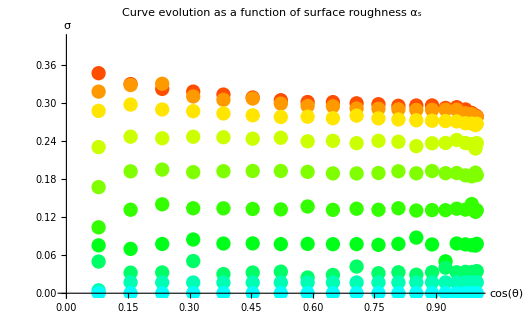

```mathematica
paramsScale0=paramsScale[[1]]; (* We only work on albedo = 1 *)
parmsScaleCurves= Table[Table[{Cos[(i-1)/resX*π/2],paramsScale0[[j]][[i]]},{i,1,resX}],{j,1,resY}];
Show[Table[ListPlot[parmsScaleCurves[[j]],PlotRange->{0,0.4},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,resY}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0.36374 | b→-0.249428 | c→0.36835 | d→-0.198888
a→0.330432 | b→-0.0481988 | c→-0.0212338 | d→0.0216487
a→0.296035 | b→-0.0371849 | c→0.0258935 | d→-0.0169417
a→0.226419 | b→0.128179 | c→-0.245918 | d→0.127485
a→0.16348 | b→0.170854 | c→-0.289007 | d→0.143579
a→0.0964532 | b→0.233832 | c→-0.414125 | d→0.218335
a→0.0688052 | b→0.0587031 | c→-0.0979843 | d→0.0451356
a→0.0510406 | b→-0.0791531 | c→0.106076 | d→-0.043879
a→0.00239952 | b→0.0856189 | c→-0.146273 | d→0.0760679
a→1.×10^-6 | b→1.83139×10^-21 | c→-4.64794×10^-21 | d→2.31341×10^-21)

Now let’s try and fit the individual parameters using another fitting for each one:

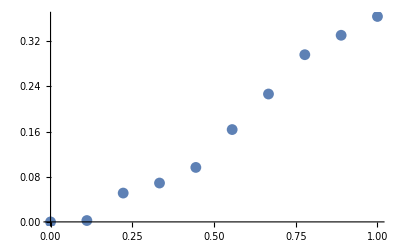

```mathematica
paramsScaleA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleA]
ListPlot[paramsScaleB];
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

All curves seem to behave the same way so let’s simply start with coefficient a:

0.00353499-0.0651119 α+0.937171 α^2-0.507038 α^3

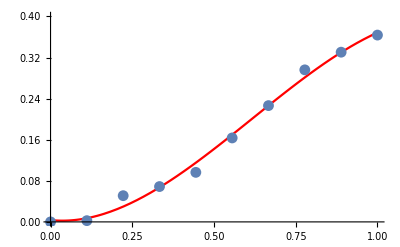

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsScaleA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,0.4}],
ListPlot[paramsScaleA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-0.282143 | c→0.428566 | d→-0.231567
a→0. | b→-0.0454623 | c→-0.0262707 | d→0.0243823
a→0. | b→0.063191 | c→-0.158864 | d→0.0833268
a→0. | b→0.128209 | c→-0.245975 | d→0.127516
a→0. | b→0.128796 | c→-0.211593 | d→0.101565
a→0. | b→0.106474 | c→-0.179701 | d→0.0911125
a→0. | b→0.0697293 | c→-0.11828 | d→0.05615
a→0. | b→0.0652507 | c→-0.159722 | d→0.10037
a→0. | b→0.0531822 | c→-0.0865683 | d→0.043666
a→0. | b→-0.0240049 | c→0.0441849 | d→-0.0239793)

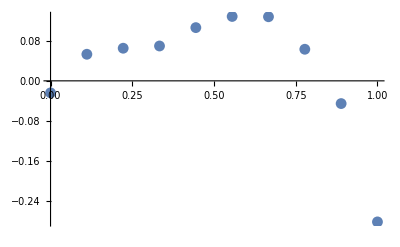

```mathematica
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleB]
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

0.00114768-0.00933862 α+1.36706 α^2-1.62417 α^3

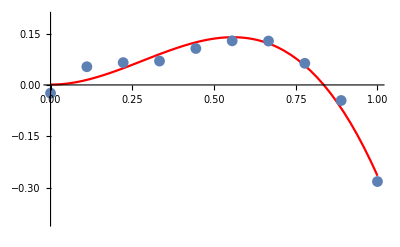

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+c*u^2+d*u^3;
fittingB = FindFit[ paramsScaleB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{-0.4,0.2}],
ListPlot[paramsScaleB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-4.44089×10^-16 | c→0.381921 | d→-0.201146
a→0. | b→-3.46945×10^-17 | c→0.0353608 | d→-0.0158126
a→0. | b→1.38778×10^-16 | c→-0.140848 | d→0.0715769
a→0. | b→2.22045×10^-16 | c→-0.226749 | d→0.114977
a→0. | b→3.33067×10^-16 | c→-0.240959 | d→0.120717
a→0. | b→2.22045×10^-16 | c→-0.229477 | d→0.123575
a→0. | b→1.11022×10^-16 | c→-0.173802 | d→0.0923607
a→0. | b→1.11022×10^-16 | c→-0.114042 | d→0.0705786
a→0. | b→-2.08167×10^-17 | c→0.0198517 | d→-0.025739
a→0. | b→2.77556×10^-17 | c→-0.0254804 | d→0.021455)

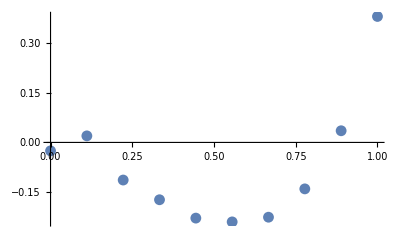

```mathematica
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleC]
ListPlot[paramsScaleD];
```

-0.00810879+0.0555568 α-2.45133 α^2+2.77709 α^3

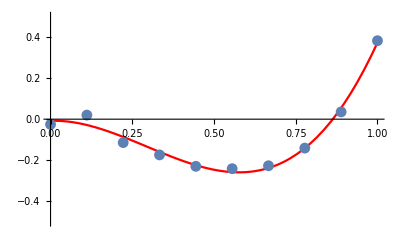

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+d*u^3;
fittingC = FindFit[ paramsScaleC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-0.5,0.5}],
ListPlot[paramsScaleC]
]
```

#### Replacing C and Fitting the D Coefficient

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→-0.191732
a→0. | b→0. | c→0. | d→-0.0368722
a→0. | b→0. | c→0. | d→0.0719149
a→0. | b→0. | c→0. | d→0.126817
a→0. | b→0. | c→0. | d→0.138742
a→0. | b→0. | c→0. | d→0.117471
a→0. | b→0. | c→0. | d→0.0764862
a→0. | b→0. | c→0. | d→0.0406583
a→0. | b→0. | c→0. | d→0.026366
a→0. | b→0. | c→0. | d→0.00269216)

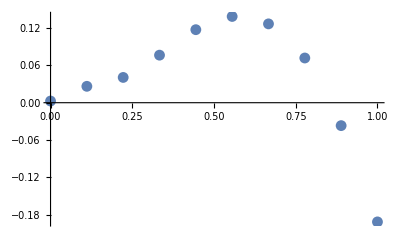

```mathematica
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleD]
```

0.00603426-0.0323576 α+1.27391 α^2-1.44299 α^3

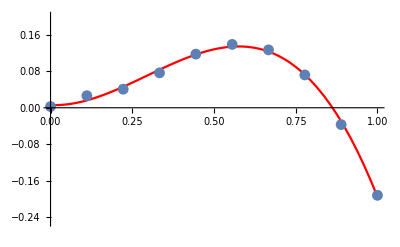

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+c*u^2+d*u^3;
fittingD = FindFit[ paramsScaleD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{-0.25,0.2}],
ListPlot[paramsScaleD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)=0.00353499-0.0651119 α+0.937171 α^2-0.507038 α^3
	b(α_s)= 0.00114768-0.00933862 α+1.36706 α^2-1.62417 α^3
	c(α_s)= -0.00810879+0.0555568 α-2.45133 α^2+2.77709 α^3
	d(α_s)=0.00603426-0.0323576 α+1.27391 α^2-1.44299 α^3
	
	σ(μ,σ_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ,fA,fB,fC,fD]
fA[α_]= 0.0035349949909801925-0.06511188079685822 α+0.93717076854373 α^2-0.5070377341283971 α^3
fB[α_]= 0.0011476761249665881-0.009338622066146229 α+1.367056254807781 α^2-1.6241668003876253 α^3
fC[α_]= -0.008108785416527653+0.05555678872279081 α-2.451331432821062 α^2+2.777088778269448 α^3
fD[α_]=0.0060342610531750685-0.03235759602633398 α+1.2739115646980932 α^2-1.4429856145300919 α^3
fScale[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];

(* Order 2 *)
fA[α_]= 0.016673375075225604-0.525209545615772 α+5.24220269537287 α^2-3.5690085024568186 α^3
fB[α_]= -0.10099003574844712+7.225961805352702 α-19.49049342659228 α^2+10.769848952215131 α^3
fC[α_]= 0.13982571795990942-11.429145510606348 α+30.177292378971725 α^2-16.789426306986503 α^3
fD[α_]=-0.065024475640786+5.731247014927747 α-14.997450899818153 α^2+8.3291032822247 α^3
fScale2[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;

Show[
Plot3D[fScale[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ"},PlotLabel->"Lobe Scale factor",PlotRange->{0,0.5}],
Plot3D[0.35*fScale2[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ"},PlotLabel->"Lobe Scale factor",PlotRange->{0,0.5},PlotStyle->Red]
]
```

(0.00114768-0.00933862 α+1.36706 α^2-1.62417 α^3) (0.00603426-0.0323576 α+1.27391 α^2-1.44299 α^3) (0.00353499-0.0651119 α+0.937171 α^2-0.507038 α^3) (-0.00810879+0.0555568 α-2.45133 α^2+2.77709 α^3)

(0.139826-11.4291 α+30.1773 α^2-16.7894 α^3) (0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3) (-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3) (-0.10099+7.22596 α-19.4905 α^2+10.7698 α^3)

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsScale0,PlotRange->{0,0.4},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fScale[Cos[(i-1)/resX π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Great!
Now we only need to find the dependence between the scale and the albedo...

# Dependence of Scale σ on albedo ρ

We try to fit our scale model to all albedo using the “amp” free coefficient to see how the amplitude is related to ρ:

```mathematica
paramsScaleMuAlpha = Table[
	Table[
		{ Cos[Mod[i,resX]/resX*π/2], 1-Quotient[i,resX]/(resY-1),paramsScale[[albedo]][[1+Quotient[i,resX]]][[1+Mod[i,resX]]]},{i,0,resX*resY-1}]
, {albedo,1,resZ}];
paramsScaleMuAlpha[[1]];
ListPlot3D[paramsScaleMuAlpha[[1]]];
```

{{amp→1.},{amp→0.682449},{amp→0.477768},{amp→0.597516},{amp→0.376276},{amp→0.131775},{amp→0.00982835},{amp→4.17205×10^-6}}

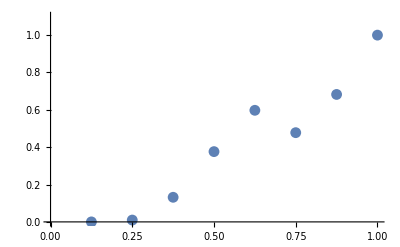

```mathematica
modelRho=amp * fScale[μ,α];
fittingRho = Table[FindFit[ paramsScaleMuAlpha[[albedo]],{modelRho},{amp},{μ,α} ],{albedo,1,resZ}]
listAmps=Table[{1-(albedo-1)/resZ, amp/.fittingRho[[albedo]]},{albedo,1,resZ}];
ListPlot[listAmps,PlotRange->{0,1.1}]
```

{a→0.,b→-0.0707083,c→1.65001,d→-0.64544}

-0.0707083 ρ+1.65001 ρ^2-0.64544 ρ^3

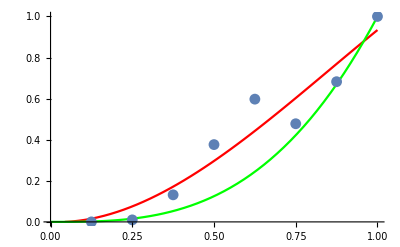

```mathematica
modelAmp=0*a+b*u+c*u^2+d*u^3;
fittingAmp=FindFit[listAmps,modelAmp,{a,b,c,d},u]
fAmp[ρ_]=Evaluate[modelAmp/.fittingAmp/.u->ρ]
fAmp2[ρ_]=ρ^3;
Show[
Plot[fAmp[ρ],{ρ,0,1},PlotStyle->Red,PlotRange->{0,1}],
Plot[fAmp2[ρ],{ρ,0,1},PlotStyle->Green,PlotRange->{0,1}],
ListPlot[listAmps]
]
```

Final Expression

We obtain the final expression for the scale parameter σ :

	a(α_s)=0.00353499-0.0651119 α+0.937171 α^2-0.507038 α^3
	b(α_s)= 0.00114768-0.00933862 α+1.36706 α^2-1.62417 α^3
	c(α_s)= -0.00810879+0.0555568 α-2.45133 α^2+2.77709 α^3
	d(α_s)=0.00603426-0.0323576 α+1.27391 α^2-1.44299 α^3
	
	σ(μ,σ_s, ρ) = ρ^3 [ a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3]

```mathematica
fScale2[μ_,α_,ρ_] = ρ^3 * fScale[μ,α];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScaleMuAlpha[[albedo]],{ PlotRange->{0,0.4},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,6}],
Table[Plot3D[fScale2[μ,α,1-(albedo-1)/resZ],{μ,0,1},{α,0,1},{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->Red],{albedo,1,6}]
]
```

-Graphics3D-

And we’re done with a very good match for scale!